# when doing nAve>1, I have to multiple pAve * nAve again (st power spectral density amplitude is independent of nAve)

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
filename="t0007ch2.csv";
data0=Import[filename];
us=10^-6;
```

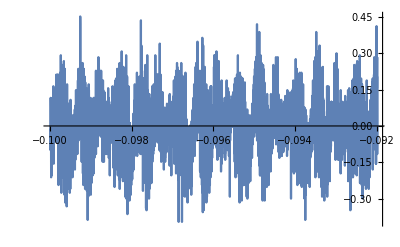

```mathematica
data=data0[[17;;-2,{1,2}]];
n=Length[data];

Δt=data[[2,1]]-data[[1,1]];

t=Range[0,n-1]Δt;
rbw=1/(n Δt);
f=Range[0,n-1]rbw;

ListPlot[data[[;;5000]],Joined->True]
```

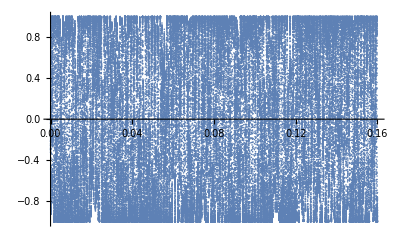

```mathematica
τ=3.7555us;
FWHM=1/(π τ);
fpkpk=FWHM/√3;
Vpkpk=1.25;
HzPerVolt=fpkpk/Vpkpk;
F= HzPerVolt data[[;;,2]];
F=F-Mean[F];
ϕ=2π Accumulate[F] Δt;
Efield=Exp[I ϕ];
ListPlot[Thread[{t,Im[Efield]}][[;;100000]]]
```

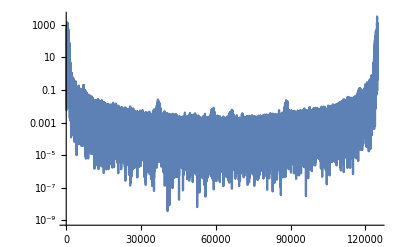

```mathematica
ListLogPlot[Abs[Fourier[Efield]]^2,Joined->True,PlotRange->All]
```

```mathematica
Clear[fAve,p,pAve,rbw];

(*gives averaged, one sided power spectrum in units of X^2/Hz*)
fftAve[Efield0_,Δt0_,nAve0_]:=Module[{Efield=Efield0,Δt=Δt0,nAve=nAve0},
n=Length[Efield];
lenAve=n/nAve;

rbwAve=1/(lenAve Δt) ;
(*partition into nAve sections of length lenAve*)
EfieldPart=Partition[Efield,lenAve];

p=Abs[√lenAve Δt Fourier[#]]^2&/@EfieldPart;

(*average and take 1 sided*)
pAve=2Total[p]/nAve;

pAve=pAve*nAve; (*not sure if this is legit but I need to remultiply by nAve to get the right voltage... othewise the PSD goes down artificially depending on the numebr of averages which affects the linewidth determination.*)

fAve=rbwAve Range[0,Floor[lenAve/2]];

Thread[{fAve,pAve[[;;Floor[lenAve/2]+1]]}]
];
```

```mathematica
(*compare integrals of A^2 *)

nAve=1;
PSDefield=fftAve[Efield,Δt,nAve]; (*in 1^2/Hz?*)
PSDf=fftAve[F ,Δt,nAve]; (*in Hz^2/Hz?*)

rbw=PSDefield[[2,1]]-PSDefield[[1,1]];

Total[Abs[Efield]^2]Δt/(Total[PSDefield[[;;,2]]]rbw)

(Total[Abs[F]^2]Δt)/(Total[PSDf[[;;,2]]]rbw)

(*should be roughly equal to 1*)
```

1.14784

1.

filename | n averages | rbw[Hz] | fraction of E field power in 0 Hz bin | fwhm[Hz]
t0007ch2.csv | 1 | 5. | 0.00150318 | 2524.24

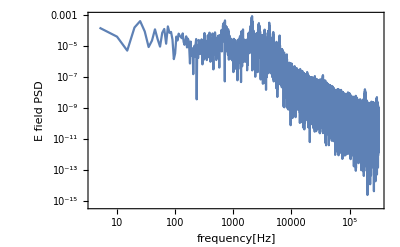

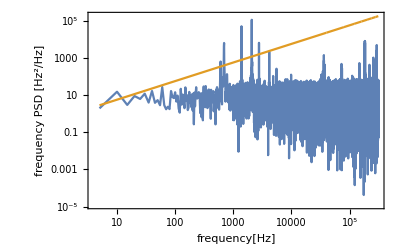

```mathematica
PSDefield=fftAve[Efield,Δt,nAve];
PSDf= fftAve[F ,Δt,nAve];
f=PSDf[[;;,1]];
β[f_]:=8Log[2]f/π^2;
βlist=Table[{ff,β[ff]},{ff,f}];

P0=PSDefield[[1,2]] / Total[PSDefield[[;;,2]]];
dataDiff=Thread[{f,PSDf[[;;,2]]-βlist[[;;,2]]}]; 

A=Total[Boole[Positive[dataDiff[[1;;,2]]]]PSDf[[1;;,2]]]rbw; (*area under curve*)


fwhm=√(8 Log[2] A);
{{"filename","n averages","rbw[Hz]","fraction of E field power in 0 Hz bin","fwhm[Hz]"},{filename,nAve,rbw,P0,fwhm}}//TableForm

nPlot=-1;
ListLogLogPlot[PSDefield[[;;nPlot]],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{"frequency[Hz]","E field PSD"},LabelStyle->{Black,12}]
ListLogLogPlot[{PSDf[[;;nPlot]],βlist},PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{"frequency[Hz]","frequency PSD [Hz^2/Hz]"},LabelStyle->{Black,12}]
```